# Figure 4B, mutS column

### This notebook generates the above figure panels . It uses pre-processed data generated by process_ODs.nb

## Helper functions

```mathematica
SetDirectory[NotebookDirectory[]]

ksround=0.01; (* round-off parameters for the KS test for the least-frequent strain data *)

SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
Clear[DispPval]
DispPval[p_]:=Which[p<0.001,"<0.001",p<0.01,ToString[NumberForm[p,{2,4}]],p<0.1,ToString[NumberForm[p,{2,3}]],p<1,ToString[NumberForm[p,{2,2}]],p==1,"p=1.0"]

SetOptions[{ListPlot,ListLogPlot,ListLinePlot,Histogram,Graphics},BaseStyle->FontSize->24,Frame->True,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}];

Clear[NaiveMinimization]
NaiveMinimization[fun_,a0_,b0_,ϵ_]:=Module[{a,b,c,d,fa,fb,fc,fd,gr=1.(Sqrt[5]+1)/2},a=1.a0;b=1.b0;Do[
c=b-(b-a)/gr;
d=a+(b-a)/gr;
fa=fun[a];fb=fun[b];fc=fun[c];fd=fun[d];
If[fc<fd,b=d;fb=fd,a=c;fa=fc];
Print[a," ",b, " fa=",fc," fb=",fb];
If[(b-a)<ϵ,Break[]]
,{n,10}];
Return[(a+b)/2]]

Clear[FisherExactTest]
FisherExactTest[succ1_,n1_,succ2_,n2_]:=1.(n1! n2! (n1+n2-succ1-succ2)! (succ1+succ2)!)/((n1+n2)! (n1-succ1)! succ1! (n2-succ2)! succ2!)
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor

## Data import and model parameters:

```mathematica
<<("turb_str_mutS_long_runs_ODvsTIME.mx");
dataSTRlong=data;
Length[dataSTRlong]

<<("turb_str_mutS_long_runs.mx");
paramsSTRlong=alldata;

<<("turb_str_mutS_short_runs.mx")
paramsSTRshort=alldata;
Print[Length[paramsSTRshort[[1]]]]

experfractions={46./(46+317),82./(82+264),122./(122+182),0.};
cfus={10,12,14,6} (* only large colonies *)

tmax=30;odcrit=0.1;
odregrowth=0.05;dilf=0.75;

(* for plotting and simulations *)
tregrowthbin={10,26,2};
tregrowthpmax=0.4;
cfusbin={0,20,1};
cfuspmax=0.25;
noreps="1000" ;(* number of replicate simulations *)
```

4

4

{10,12,14,6}

## Plotting functions

```mathematica
Clear[MakeBar2,MakeBarFromNM,RegrowthProbPlot,RegrowtTimeDistribution,LeastAbundantStrain]
MakeBar2[x_,y1_,y2_]:={AbsolutePointSize[10],Point[{x,(y1+y2)/2}],AbsoluteThickness[2],Line[{{x-0.25,y1},{x+0.25,y1}}],Line[{{x-0.25,y2},{x+0.25,y2}}],AbsoluteThickness[1],Line[{{x-0.15,y1},{x+0.15,y1}}],Line[{{x-0.15,y2},{x+0.15,y2}}],Line[{{x,y1},{x,y2}}]};
MakeBarFromNM[x_,n_,m_]:=MakeBar2[x,(m+1/2z^2)/(n+z^2)-z/(n+z^2)Sqrt[m (n-m)/n+z^2/4],(m+1/2z^2)/(n+z^2)+z/(n+z^2)Sqrt[m (n-m)/n+z^2/4]]/.z->1 (* Wilson score interval https://en.wikipedia.org/wiki/Binomial_proportion_confidence_interval *)
RegrowthProbPlot[name_]:=Module[{gr,pval,pexp,pth,muypos},
pval=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
pexp=Length[Select[tregrowths,NumberQ[#1]&]]/Length[tregrowths];
pth=Length[Select[tmp,NumberQ[#1⟦2⟧]&]]/Length[tmp];
muypos=If[pexp>0.4 && pth>0.4,0.1,If[(pexp>0.5 && pth<0.5) || (pexp<0.5 && pth>0.5),0.5,1 ]];
gr=Graphics[{MakeBarFromNM[0.7,Length[tregrowths],Length[Select[tregrowths,NumberQ[#]&]]],Darker[Green],MakeBarFromNM[1.5,Length[tmp],Length[Select[tmp,(NumberQ[#[[2]]]&)]]]},(*Epilog->{Text["g_s",{0.7,0}],Text["g_r",{1.5,0}]},*)Axes->{None,Automatic},PlotRange->{{0,2},{0,1}},Axes->True,Frame->False,AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AspectRatio->1.3,ImageSize->200,PlotLabel->Style[("p_value= "<>DispPval[pval]),24],Epilog->(Style[Text[TextGrid[{{"μ="},{Read[StringToStream[mutrate],Number]}},Alignment->Center],{1,muypos}](*TextGrid[{{"μ=",Read[StringToStream[mutrate],Number]}}]*),24])];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"]]


RegrowtTimeDistribution[name_]:=Module[{gr,pval,grth,grexp},
grth=SmoothHistogram[Select[tmp,((NumberQ[#[[2]]])&)][[All,2]],Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom];
grexp=Histogram[Select[tregrowths-ainjs,(#≠∞)&],tregrowthbin,"PDF",ChartStyle->Opacity[0.5,Black]];
gr=Show[{grexp,grth}(*Epilog->{Red,PointSize[0.02],(Point[{#,0.02}]&/@Select[tregrowths-Ainjs[[All,1,1]],(#≠∞)&])}*),Frame->True,FrameLabel->{"t_regrowth - t_0 [h]",None},AspectRatio->1,ImageSize->200(*,ChartLegends->{"sim","exp"}*),PlotRange->{0,tregrowthpmax},PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Select[tmp[[All,2]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]]]),24]];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];
pval=KolmogorovSmirnovTest[Select[tmp[[All,2]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]];
Print["KS-test p-value: ",pval]]

LeastAbundantStrain[name_]:=Module[{fractions,gr},
If[Length[simdist[[1,1]]]==8,
fractions=Table[Min[1.#[[6]]/(#[[8]]+#[[6]]),1.#[[8]]/(#[[8]]+#[[6]])]&/@Select[simdist[[i]],(#[[6]]+#[[8]]>0)&],{i,Length[simdist]}]
,If[Length[simdist[[1,1]]]==10,fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}],Print["incorrect format"];Abort[]]];
gr=Histogram[{Flatten[fractions],experfractions},{0,0.5,0.1},"PDF",ScalingFunctions->{"Linear","Linear"},PlotRange->All,ChartStyle->{Darker[Green],Black},Frame->True,FrameTicks->{{{0,2,4,6,8},Automatic},{{0,0.25,0.5},Automatic}},FrameLabel->{"fraction",None(*"PDF"*)},ImageSize->200,(*ChartLegends->{"sim","exp"},*)AspectRatio->1,PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Round[Flatten[fractions],ksround],Round[experfractions,ksround]]]),24]];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];
Print["fraction below 0.1 (exp):",1.Length[Select[experfractions,(#<0.1)&]]/Length[experfractions]];
Print["fraction below 0.1 (sim):",1.Length[Select[Flatten[fractions],(#<0.1)&]]/Length[Flatten[fractions]]];
]

Clear[HistogramMutants]
HistogramMutants[namepart_,strains_,alleles_,output_,range_:{{0,cfusbin[[2]]},{0,cfuspmax}}]:=Module[{types=Table[Number,{strains*(alleles+1)}],simcfus,thcfus},
(* this simpler method ignores fitting the tfirstthr times, but works nevertheless and is much faster *)
simcfus=Table[ReadList[namepart<>ToString[n]<>".dat",types],{n,Length[births2]}];
Print[Length[simcfus]];
thcfus=Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]];
pl=Show[{Histogram[cfus,cfusbin,"PDF",ChartStyle->Gray],SmoothHistogram[thcfus,Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom,Frame->True,FrameLabel->{"n_r",None(*"PDF"*)},PlotRange->range]},PlotRange->range,AspectRatio->1,ImageSize->200,PlotLabel->Style[
"p_value= "<>DispPval[KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus]]
,24]];
Print[pl];
Export[output,pl,"PNG"]
]
```

### Function that will be maximized when fitting the model to three data types:

```mathematica
Clear[FittingFunction]
FittingFunction[pval1_,pval2_,pval3_]:=pval1-If[pval2<0.1,100(0.1-pval2),0]-If[pval3<0.1,100(0.1-pval3),0]  (* same as for RIF *)
```

## Simple model for STR. One resistant allele. Mixed strains AD30 and AD30YFP .

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsSTRlong;
Length[vols]
Do[If[birthsres[[i,1]]==0,tregrowths[[i]]=∞],{i,Length[births]}]
tregrowths
Print["max. time to end = ",Max[Select[tends,NumberQ]]]

{vols2,births2,odinis2,tfirstthr2,tends2}=paramsSTRshort;
Length[vols2]
odcrit2=0.1;
dilf2=0.75;
```

4

{19.9423,22.2021,20.4965,19.6207}

max. time to end = 23.8308

4

```mathematica
valid=(Position[birthsres[[All,1]],#]&/@Select[birthsres[[All,1]],(NumberQ[#] && Abs[#]<2.5 && Abs[#]>0)&])[[All,1,1]]
```

{1,2,3,4}

### Prepare the input for the simulation:

```mathematica
mutrate="4.0e-9";  (* value from fluctuation test for AD30mutS and EEL02mutS *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\STRmutS\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->1234]
```

4.×10^-9

### Run the simulation :

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS"]

args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STRmutS

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 4 13 fixed_mu_2strains_1 24.93 0.00217597 5.09744 23.8306 19.9423 0.05 1000 4.e-9 4.e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.75 0.00137953 5.8845 23.8307 22.2021 0.05 1000 4.e-9 4.e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.3 0.00232933 5.02 23.8307 20.4965 0.05 1000 4.e-9 4.e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 24.44 0.00188214 4.98442 23.8308 19.6207 0.05 1000 4.e-9 4.e-9 0.75 input_params_4.dat 0.1

0

### Make plots:

0.951317

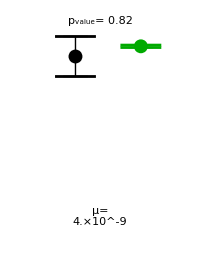

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STRmutS_2allele_no_lag_Pregrowth.png

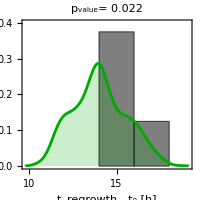

KS-test p-value: 0.0220469

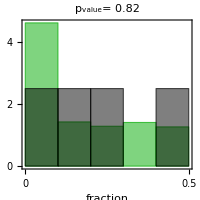

fraction below 0.1 (exp):0.25

fraction below 0.1 (sim):0.461718

```mathematica
simdist=Table[Import["models\\STRmutS\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["STRmutS_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["STRmutS_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["STRmutS_2allele_no_lag_LBS.png"]
```

### Short - term experiment:

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\STRmutS\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

4.×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS"]
args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_STR"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STRmutS

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 4 13 preexist_res_2strains_1_allele_4.0e-9_STR1 25.74 0.00330139 100 5.02175 100 0.05 1000 4.e-9 4.e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_4.0e-9_STR2 25.37 0.00288378 100 5.02178 100 0.05 1000 4.e-9 4.e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_4.0e-9_STR3 24.44 0.00330558 100 5.02183 100 0.05 1000 4.e-9 4.e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_4.0e-9_STR4 24.42 0.0029249 100 5.02189 100 0.05 1000 4.e-9 4.e-9 0.75 input_params_4.dat  0.1

0

4

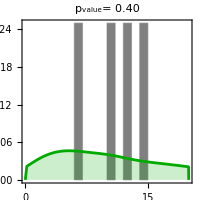

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STRmutS_2allele_no_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\STRmutS\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_STR",strains,alleles,NotebookDirectory[]<>"\\figures\\STRmutS_2allele_no_lag_Nmut.png"]
```

### Find the optimal mu that maximizes the p - value of the fit to the large-colony mutant number distribution:

```mathematica
Clear[RunOnce,mu]
RunOnce[mu_]:=RunOnce[mu]=Module[{pval,simcfus,processes},
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS"];
args=Table[
{"optimization"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],"100",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];
(*Run["powershell -NoExit "<>name]*)
ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)
simcfus=Table[ReadList["strains_optimization"<>ToString[n]<>".dat",{Number,Number,Number,Number}],{n,Length[births2]}];
SetDirectory[NotebookDirectory[]];
pval=KolmogorovSmirnovTest[Flatten[Table[Table[Total[simcfus[[k,i,3;;]]],{i,Length[simcfus[[k]]]}],{k,Length[simcfus]}]],cfus];
Return[-pval]]
```

```mathematica
NaiveMinimization[RunOnce,10^-9,10^-8,10^-10]
```

1.×10^-9 6.56231×10^-9 fa=-0.149695 fb=-0.00971956

1.×10^-9 4.43769×10^-9 fa=-0.579179 fb=-0.149695

2.31308×10^-9 4.43769×10^-9 fa=-0.165881 fb=-0.149695

2.31308×10^-9 3.62616×10^-9 fa=-0.579179 fb=-0.315261

2.81464×10^-9 3.62616×10^-9 fa=-0.557972 fb=-0.315261

2.81464×10^-9 3.31619×10^-9 fa=-0.579179 fb=-0.577655

3.00621×10^-9 3.31619×10^-9 fa=-0.553664 fb=-0.577655

3.12461×10^-9 3.31619×10^-9 fa=-0.579179 fb=-0.577655

3.12461×10^-9 3.24301×10^-9 fa=-0.673893 fb=-0.61299

3.16984×10^-9 3.24301×10^-9 fa=-0.671725 fb=-0.61299

3.20642×10^-9

### We will use this new value of μ in the next model below.

## Single allele model for STR, fitted to the mutant distribution data

```mathematica
mutrate="3.2e-9";  (* NEW value from fitting the data *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\STRmutS_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->1234]
```

3.2×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS_fitted"]
args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STRmutS_fitted

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 4 13 fixed_mu_2strains_1 24.93 0.00217597 5.09744 23.8306 19.9423 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.75 0.00137953 5.8845 23.8307 22.2021 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.3 0.00232933 5.02 23.8307 20.4965 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 24.44 0.00188214 4.98442 23.8308 19.6207 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_4.dat 0.1

0

0.90774

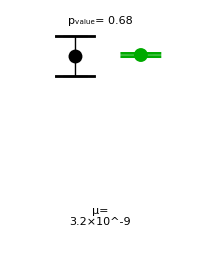

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STRmutS_fitted_2allele_no_lag_Pregrowth.png

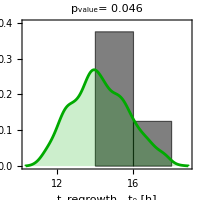

KS-test p-value: 0.046248

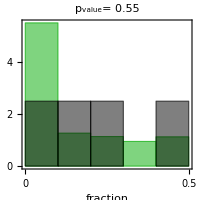

fraction below 0.1 (exp):0.25

fraction below 0.1 (sim):0.551289

```mathematica
simdist=Table[Import["models\\STRmutS_fitted\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["STRmutS_fitted_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["STRmutS_fitted_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["STRmutS_fitted_2allele_no_lag_LBS.png"]
```

### Short - term experiment:

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\STRmutS_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"Generic",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

3.2×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS_fitted"]
args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_STR"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STRmutS_fitted

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 4 13 preexist_res_2strains_1_allele_3.2e-9_STR1 25.74 0.00330139 100 5.02175 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_3.2e-9_STR2 25.37 0.00288378 100 5.02178 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_3.2e-9_STR3 24.44 0.00330558 100 5.02183 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_3.2e-9_STR4 24.42 0.0029249 100 5.02189 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_4.dat  0.1

0

4

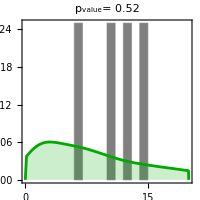

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STRmutS_fitted_2allele_no_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\STRmutS_fitted\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_STR",strains,alleles,NotebookDirectory[]<>"\\figures\\STRmutS_fitted_2allele_no_lag_Nmut.png"]
```

## Single allele model for STR with filamentation, with the same (fitted) μ as the model above.

```mathematica
mutrate="3.2e-9";  (* NEW value from fitting the data *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;

BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={births[[nn,1]]{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\STRmutS_filament_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->1234]
```

3.2×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS_filament_fitted"]

args=Table[
{"fixed_mu_2strains_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1"},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STRmutS_filament_fitted

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 4 13 fixed_mu_2strains_1 24.93 0.00217597 5.09744 23.8306 19.9423 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_1.dat 0.1 fixed_mu_2strains_2 25.75 0.00137953 5.8845 23.8307 22.2021 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_2.dat 0.1 fixed_mu_2strains_3 25.3 0.00232933 5.02 23.8307 20.4965 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_3.dat 0.1 fixed_mu_2strains_4 24.44 0.00188214 4.98442 23.8308 19.6207 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_4.dat 0.1

0

0.856551

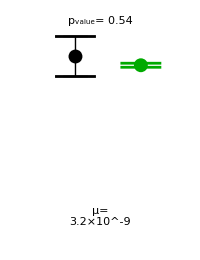

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STRmutS_filam_fitted_2allele_no_lag_Pregrowth.png

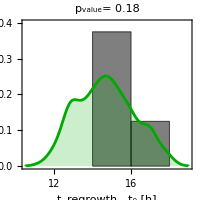

KS-test p-value: 0.180467

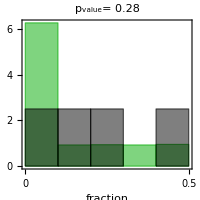

fraction below 0.1 (exp):0.25

fraction below 0.1 (sim):0.626192

```mathematica
simdist=Table[Import["models\\STRmutS_filament_fitted\\distribution_fixed_mu_2strains_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["STRmutS_filam_fitted_2allele_no_lag_Pregrowth.png"]
RegrowtTimeDistribution["STRmutS_filam_fitted_2allele_no_lag_Tregrowth.png"]
LeastAbundantStrain["STRmutS_filam_fitted_2allele_no_lag_LBS.png"]
```

### Short - term experiment:

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\STRmutS_filament_fitted\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],mt[[1]],wt[[2]],mt[[2]],{"end"}],"Table"]
,{nn,Length[vols2]}]
```

3.2×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS_filament_fitted"]

args=Table[
{"preexist_res_2strains_1_allele_"<>mutrate<>"_STR"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1"},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STRmutS_filament_fitted

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_ind_params.exe 4 13 preexist_res_2strains_1_allele_3.2e-9_STR1 25.74 0.00330139 100 5.02175 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_1.dat  0.1 preexist_res_2strains_1_allele_3.2e-9_STR2 25.37 0.00288378 100 5.02178 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_2.dat  0.1 preexist_res_2strains_1_allele_3.2e-9_STR3 24.44 0.00330558 100 5.02183 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_3.dat  0.1 preexist_res_2strains_1_allele_3.2e-9_STR4 24.42 0.0029249 100 5.02189 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_4.dat  0.1

0

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\STRmutS_filament_fitted\\strains_preexist_res_2strains_1_allele_"<>mutrate<>"_STR",strains,alleles,NotebookDirectory[]<>"\\figures\\STRmutS_filam_fitted_2allele_no_lag_Nmut.png"]
```

4

-Graphics-

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STRmutS_filam_fitted_2allele_no_lag_Nmut.png

## Phenotypic lag model for STRmutS. One resistant allele. Mixed strains AD30mutS and AD30YFPmutS .

### This model does not improve the fit but we consider it here for comparison with the no - lag model.

```mathematica
mutrate="3.2e-9";  (* value as in the no-lag fitted model *)
lagrate="0.6" ; (* this must be experimentally chosen to give the best fit *)
intgrfraction=0.5; (* this must be experimentally chosen to give the best fit *)
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
BlockRandom[Do[
(* parent strains before and after the antibiotic *)
wt={{births[[nn,1]],births[[nn,1]]},{0,0}};
(* intermediate strains before and after the antibiotics*)
it={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{intgrfraction,intgrfraction}}; 
(* mutant strains before and after the antibiotic *)
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};

Export[NotebookDirectory[]<>"\\models\\STRmutS_filament_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123]
```

3.2×10^-9

```mathematica
Clear[nn]
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS_filament_lag"]

args=Table[
{"fixed_mu_2strains_lag_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",lagrate},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name]

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STRmutS_filament_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 4 14 fixed_mu_2strains_lag_1 24.93 0.00217597 5.09744 23.8306 19.9423 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_1.dat 0.1 0.6 fixed_mu_2strains_lag_2 25.75 0.00137953 5.8845 23.8307 22.2021 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_2.dat 0.1 0.6 fixed_mu_2strains_lag_3 25.3 0.00232933 5.02 23.8307 20.4965 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_3.dat 0.1 0.6 fixed_mu_2strains_lag_4 24.44 0.00188214 4.98442 23.8308 19.6207 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_4.dat 0.1 0.6

0

0.828431

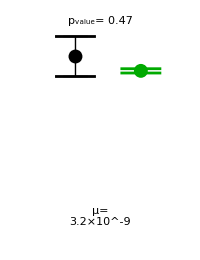

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STRmutS_filam_2allele_lag_Pregrowth.png

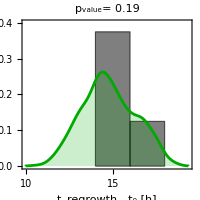

KS-test p-value: 0.190872

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STRmutS_filam_lag_params.png

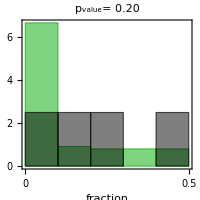

fraction below 0.1 (exp):0.25

fraction below 0.1 (sim):0.667527

```mathematica
simdist=Table[Import["models\\STRmutS_filament_lag\\distribution_fixed_mu_2strains_lag_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
1.Length[Select[tmp,(NumberQ[#[[2]]]&)]]/Length[tmp]

RegrowthProbPlot["STRmutS_filam_2allele_lag_Pregrowth.png"]
RegrowtTimeDistribution["STRmutS_filam_2allele_lag_Tregrowth.png"]
Export[NotebookDirectory[]<>"\\figures\\STRmutS_filam_lag_params.png",Style["μ="<>mutrate<>"\nω="<>lagrate<>"\nq="<>ToString[intgrfraction],FontSize->32],"PNG",ImageSize->300]
LeastAbundantStrain["STRmutS_filam_2allele_lag_LBS.png"]
```

### Now optimize ω and q. The values are then copied manually to the code above.

```mathematica
Clear[RunOnce2,ω,q]
mu=Interpreter["Number"][mutrate]
RunOnce2[ω_?NumericQ,q_?NumericQ]:=RunOnce2[ω,q]=Module[{pval1,pval2,pval3,fractions,simcfus,simdist,tmp,psurv,psurvexp,ret,processes},
(*Return[ω^2+q^2]*)
strains=2;alleles=1;
BlockRandom[Do[
wt={{births[[nn,1]],births[[nn,1]]},{0,0}};
it={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{Abs[q],Abs[q]}}; 
mt={births[[nn,1]]{1,1},If[birthsres[[nn,1]]>0,birthsres[[nn,1]],RandomChoice[Select[birthsres[[All,1]],(#>0)&]]]{1,1}};
Export[NotebookDirectory[]<>"\\models\\STRmutS_filament_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols]}],RandomSeeding->123];
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS_filament_lag"];

args=Table[
{"optimization_"<>ToString[nn],ToString[vols[[nn]]],ToString[odinis[[nn]]],ToString[ainjs[[nn]]],ToString[tends[[nn]]],ToString[If[tregrowths[[nn]]≠∞,tregrowths[[nn]],tmax]],ToString[odregrowth],"300",ToString[mu,CForm],ToString[mu,CForm],ToString[dilf],("input_params_"<>ToString[nn]<>".dat"),"0.1",ToString[Abs[ω]]},{nn,Length[vols]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]];

ret=RunProcess[{"powershell",name}]; (* waits until the process exits *)

SetDirectory[NotebookDirectory[]];
simdist=Table[Import["models\\STRmutS_filament_lag\\distribution_optimization_"<>ToString[nn]<>".dat","Table"],{nn,Length[births]}];
tmp=Table[If[NumberQ[#[[2]]],{#[[1]],#[[2]]-ainjs[[i]],#[[3]],#[[4]]-ainjs[[i]]},#]&/@Select[simdist[[i]],(Abs[#[[3]]-tfirstthr[[i]]]<0.2)&],{i,Length[simdist]}];
tmp=Flatten[tmp,1];
pval2=KolmogorovSmirnovTest[Select[tmp⟦All,2⟧,NumberQ[#1]&],Select[tregrowths-ainjs,NumberQ[#1]&]];
pval1=FisherExactTest[Length[Select[tmp,NumberQ[#1⟦2⟧]&]],Length[tmp],Length[Select[tregrowths,NumberQ[#1]&]],Length[tregrowths]];
fractions=Table[Min[1.#[[7]]/(#[[10]]+#[[7]]),1.#[[10]]/(#[[10]]+#[[7]])]&/@Select[simdist[[i]],(#[[7]]+#[[10]]>0)&],{i,Length[simdist]}];
pval3=KolmogorovSmirnovTest[Flatten[fractions][[;;;;2]],experfractions];
ret=-FittingFunction[pval1,pval2,pval3];
Print["ω= ",ω," q =",q, " fun=",ret];
Return[ret]
]
```

3.2×10^-9

```mathematica
fits=Table[{ω,q,RunOnce2[ω,q]},{ω,0.1,0.7,0.1},{q,0,0.7,0.1}]
```

ω= 0.1 q =0. fun=8.76921

ω= 0.1 q =0.1 fun=9.32401

ω= 0.1 q =0.2 fun=9.17749

ω= 0.1 q =0.3 fun=7.57743

ω= 0.1 q =0.4 fun=7.09346

ω= 0.1 q =0.5 fun=5.26993

ω= 0.1 q =0.6 fun=4.58941

ω= 0.1 q =0.7 fun=2.01063

ω= 0.2 q =0. fun=6.71077

ω= 0.2 q =0.1 fun=6.83673

ω= 0.2 q =0.2 fun=6.40313

ω= 0.2 q =0.3 fun=6.53184

ω= 0.2 q =0.4 fun=4.50132

ω= 0.2 q =0.5 fun=2.13109

ω= 0.2 q =0.6 fun=1.84856

ω= 0.2 q =0.7 fun=-0.39679

ω= 0.3 q =0. fun=5.97292

ω= 0.3 q =0.1 fun=4.48947

ω= 0.3 q =0.2 fun=2.71104

ω= 0.3 q =0.3 fun=4.92295

ω= 0.3 q =0.4 fun=4.77337

ω= 0.3 q =0.5 fun=4.99806

ω= 0.3 q =0.6 fun=1.19889

ω= 0.3 q =0.7 fun=-0.307031

ω= 0.4 q =0. fun=4.54565

ω= 0.4 q =0.1 fun=5.00971

ω= 0.4 q =0.2 fun=2.24467

ω= 0.4 q =0.3 fun=1.41391

ω= 0.4 q =0.4 fun=-0.328662

ω= 0.4 q =0.5 fun=-0.445447

ω= 0.4 q =0.6 fun=-0.396023

ω= 0.4 q =0.7 fun=-0.398286

ω= 0.5 q =0. fun=4.53733

ω= 0.5 q =0.1 fun=1.09615

ω= 0.5 q =0.2 fun=4.96374

ω= 0.5 q =0.3 fun=-0.38246

ω= 0.5 q =0.4 fun=-0.27988

ω= 0.5 q =0.5 fun=-0.43382

ω= 0.5 q =0.6 fun=-0.458367

ω= 0.5 q =0.7 fun=-0.473952

ω= 0.6 q =0. fun=5.36305

ω= 0.6 q =0.1 fun=1.7484

ω= 0.6 q =0.2 fun=-0.382822

ω= 0.6 q =0.3 fun=-0.403095

ω= 0.6 q =0.4 fun=1.31971

ω= 0.6 q =0.5 fun=-0.513659

ω= 0.6 q =0.6 fun=-0.400546

ω= 0.6 q =0.7 fun=-0.457694

ω= 0.7 q =0. fun=4.01935

ω= 0.7 q =0.1 fun=1.10858

ω= 0.7 q =0.2 fun=1.22429

ω= 0.7 q =0.3 fun=3.37782

ω= 0.7 q =0.4 fun=-0.42149

ω= 0.7 q =0.5 fun=-0.506719

ω= 0.7 q =0.6 fun=-0.440902

ω= 0.7 q =0.7 fun=-0.491359

{{{0.1,0.,8.76921},{0.1,0.1,9.32401},{0.1,0.2,9.17749},{0.1,0.3,7.57743},{0.1,0.4,7.09346},{0.1,0.5,5.26993},{0.1,0.6,4.58941},{0.1,0.7,2.01063}},{{0.2,0.,6.71077},{0.2,0.1,6.83673},{0.2,0.2,6.40313},{0.2,0.3,6.53184},{0.2,0.4,4.50132},{0.2,0.5,2.13109},{0.2,0.6,1.84856},{0.2,0.7,-0.39679}},{{0.3,0.,5.97292},{0.3,0.1,4.48947},{0.3,0.2,2.71104},{0.3,0.3,4.92295},{0.3,0.4,4.77337},{0.3,0.5,4.99806},{0.3,0.6,1.19889},{0.3,0.7,-0.307031}},{{0.4,0.,4.54565},{0.4,0.1,5.00971},{0.4,0.2,2.24467},{0.4,0.3,1.41391},{0.4,0.4,-0.328662},{0.4,0.5,-0.445447},{0.4,0.6,-0.396023},{0.4,0.7,-0.398286}},{{0.5,0.,4.53733},{0.5,0.1,1.09615},{0.5,0.2,4.96374},{0.5,0.3,-0.38246},{0.5,0.4,-0.27988},{0.5,0.5,-0.43382},{0.5,0.6,-0.458367},{0.5,0.7,-0.473952}},{{0.6,0.,5.36305},{0.6,0.1,1.7484},{0.6,0.2,-0.382822},{0.6,0.3,-0.403095},{0.6,0.4,1.31971},{0.6,0.5,-0.513659},{0.6,0.6,-0.400546},{0.6,0.7,-0.457694}},{{0.7,0.,4.01935},{0.7,0.1,1.10858},{0.7,0.2,1.22429},{0.7,0.3,3.37782},{0.7,0.4,-0.42149},{0.7,0.5,-0.506719},{0.7,0.6,-0.440902},{0.7,0.7,-0.491359}}}

```mathematica
Sort[Flatten[fits,1],(#1[[3]]<#2[[3]])&]
```

{{0.6,0.5,-0.513659},{0.7,0.5,-0.506719},{0.7,0.7,-0.491359},{0.5,0.7,-0.473952},{0.5,0.6,-0.458367},{0.6,0.7,-0.457694},{0.4,0.5,-0.445447},{0.7,0.6,-0.440902},{0.5,0.5,-0.43382},{0.7,0.4,-0.42149},{0.6,0.3,-0.403095},{0.6,0.6,-0.400546},{0.4,0.7,-0.398286},{0.2,0.7,-0.39679},{0.4,0.6,-0.396023},{0.6,0.2,-0.382822},{0.5,0.3,-0.38246},{0.4,0.4,-0.328662},{0.3,0.7,-0.307031},{0.5,0.4,-0.27988},{0.5,0.1,1.09615},{0.7,0.1,1.10858},{0.3,0.6,1.19889},{0.7,0.2,1.22429},{0.6,0.4,1.31971},{0.4,0.3,1.41391},{0.6,0.1,1.7484},{0.2,0.6,1.84856},{0.1,0.7,2.01063},{0.2,0.5,2.13109},{0.4,0.2,2.24467},{0.3,0.2,2.71104},{0.7,0.3,3.37782},{0.7,0.,4.01935},{0.3,0.1,4.48947},{0.2,0.4,4.50132},{0.5,0.,4.53733},{0.4,0.,4.54565},{0.1,0.6,4.58941},{0.3,0.4,4.77337},{0.3,0.3,4.92295},{0.5,0.2,4.96374},{0.3,0.5,4.99806},{0.4,0.1,5.00971},{0.1,0.5,5.26993},{0.6,0.,5.36305},{0.3,0.,5.97292},{0.2,0.2,6.40313},{0.2,0.3,6.53184},{0.2,0.,6.71077},{0.2,0.1,6.83673},{0.1,0.4,7.09346},{0.1,0.3,7.57743},{0.1,0.,8.76921},{0.1,0.2,9.17749},{0.1,0.1,9.32401}}

### The first pair of values is the best fit.

### Short - term experiment :

```mathematica
mu=Interpreter["Number"][mutrate]
strains=2;alleles=1;
Do[
(* parent strains before and after the antibiotic *)
wt={{births2[[nn,1]],births2[[nn,1]]},{0,0}};
(* intermediate strains before and after the antibiotics*)
it=births2[[nn,1]]{{1,1},{0,0}};
(* mutant strains before and after the antibiotic *)
mt=births2[[nn,1]]{{1,1},{1,1}};
Export[NotebookDirectory[]<>"\\models\\STRmutS_filament_lag\\input_params_"<>ToString[nn]<>".dat",Join[{"CIP","0.66",strains,alleles},wt[[1]],it[[1]],mt[[1]],wt[[2]],it[[2]],mt[[2]],{1,1},{"end"}],"Table"]
,{nn,Length[vols2]}]
```

3.2×10^-9

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\STRmutS_filament_lag"]

args=Table[
{"preexist_res_2strains_1_allele_lag_"<>mutrate<>"_STR"<>ToString[nn],ToString[vols2[[nn]]],ToString[odinis2[[nn]]],ToString[100],ToString[tends2[[nn]]],ToString[100],ToString[odregrowth],noreps,ToString[mu,CForm],ToString[mu,CForm],ToString[dilf2],("input_params_"<>ToString[nn]<>".dat")," 0.1",lagrate},{nn,Length[births2]}];
name="..\\create_processes.exe ..\\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe "<>ToString[Length[args]]<>" "<>ToString[Length[args[[1]]]]<>" "<>StringJoin[Riffle[Flatten[args]," "]]
(*Run["powershell -NoExit "<>name]*)
Run["powershell "<>name];

SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STRmutS_filament_lag

..\create_processes.exe ..\turbidostat_evolution_for_Bayesian_many_strains_many_muts_interm_state_ind_params_v2.exe 4 14 preexist_res_2strains_1_allele_lag_3.2e-9_STR1 25.74 0.00330139 100 5.02175 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_1.dat  0.1 0.6 preexist_res_2strains_1_allele_lag_3.2e-9_STR2 25.37 0.00288378 100 5.02178 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_2.dat  0.1 0.6 preexist_res_2strains_1_allele_lag_3.2e-9_STR3 24.44 0.00330558 100 5.02183 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_3.dat  0.1 0.6 preexist_res_2strains_1_allele_lag_3.2e-9_STR4 24.42 0.0029249 100 5.02189 100 0.05 1000 3.2000000000000005e-9 3.2000000000000005e-9 0.75 input_params_4.dat  0.1 0.6

4

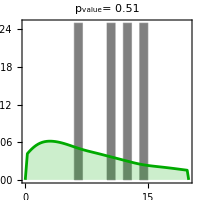

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\\figures\STRmutS_filam_2allele_lag_Nmut.png

```mathematica
HistogramMutants[NotebookDirectory[]<>"\\models\\STRmutS_filament_lag\\strains_preexist_res_2strains_1_allele_lag_"<>mutrate<>"_STR",strains,alleles+1,NotebookDirectory[]<>"\\figures\\STRmutS_filam_2allele_lag_Nmut.png"]
```